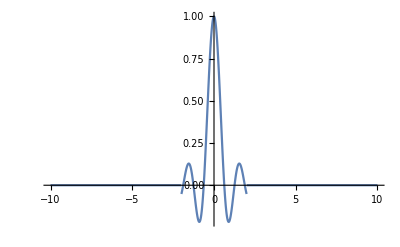

```mathematica
X1t[t] = Sinc[5t] * UnitStep [ 4- (t^2)];
Plot [ X1t[t],{t,-10,10}]
```

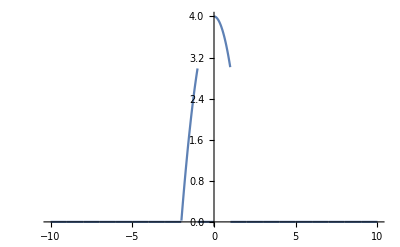

```mathematica
X2t[t_]:= ( UnitStep[Sin[Pi*t]] )* ( Ramp[4-(t^2)]);
Plot[X2t[t],{t,-10,10}]
```

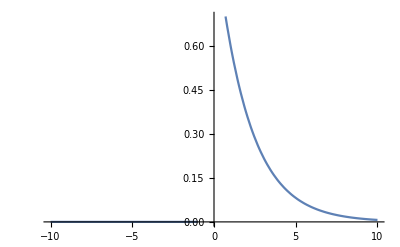

1

```mathematica
X3t[t_]:=If[t<-1, 0 , If[t< 0, 1 , Exp[-t/2]]];
Plot[X3t[t],{t,-10,10}]
X3t[-0.5]
```

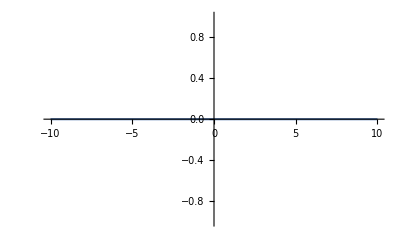

```mathematica
X3t[t_]:=If[t<-1, 0 , If[t< 0, 1 , Exp[-t/2]]];
Plot[X4t[t],{t,-10,10}]
```

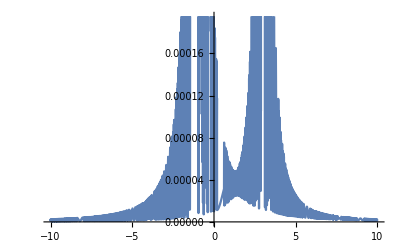

```mathematica
X4t[t_]:= (1/0.0001) * (Sinc[t/0.0001]^2);
Plot[X4t[t-3]+2*X4t[t+1],{t,-10,10}]
```

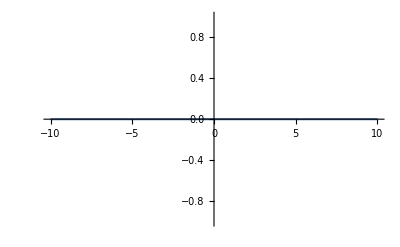

```mathematica
u[t_] := (10000 * UnitStep[t+0.0001] )- ( 10000 * UnitStep[t-0.0001]);
Plot[u[t],{t,-10,10}]
```

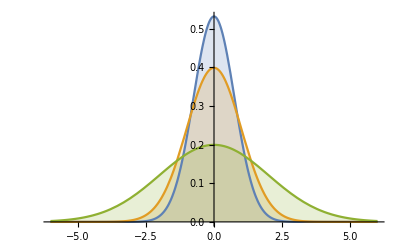

```mathematica
Plot[Table[PDF[NormalDistribution[0,s],x],{s,{0.75,1,2}}] // Evaluate, {x,-6,6} , Filling->Axis]
```

```mathematica
e[g_]:= Integrate[((g)^2),{t,-Infinity,Infinity}];
p[g_]:=Limit[(1/(2 *T)) * Integrate[((g)^2),{t, -T ,T}], T -> Infinity];
X1t[t] = Sinc[5t] * UnitStep [ 4- (t^2)];
e[X1t[t]]

Dc[g_]:=Limit[(1/(2*T)) * Integrate[g,{t,-T,T}], T -> Infinity];

Dc[Cos[2*t]^2]
```

1/50 (-1+Cos[20]+20 SinIntegral[20])

1/2

```mathematica
X1t[t] = Sinc[5t] * UnitStep [ 4- (t^2)];
e[X1t[t]]
```

1/50 (-1+Cos[20]+20 SinIntegral[20])

```mathematica
RootApproximant[1/50 (-1+Cos[20]+20 SinIntegral[20])]
```

Root[-2+2 #1^2+3 #1^3+4 #1^4-#1^5+2 #1^6-#1^7+2 #1^8+3 #1^10&,2]

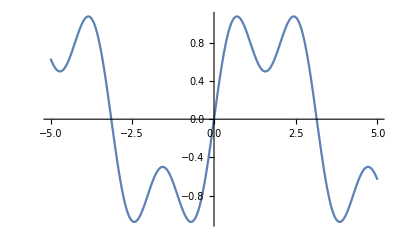

```mathematica
f[t_]:= Sin[t] + 0.5 * Sin[3 *t];
Plot[f[t],{t,-5,5}]
```

```mathematica
u[t_] := (10000 * UnitStep[t+0.0001] )- ( 10000 * UnitStep[t-0.0001]);
f[t_]:= Sin[t] + 0.5 * Sin[3 *t];
g[t_]:= (f[t] )* ( u[t]);
Plot[g[t],{t,-10,10}]
```

-Graphics-

```mathematica
u[t_] := (10000 * UnitStep[t+0.0001] )- ( 10000 * UnitStep[t-0.0001]);
f[t_]:= Sin[t] + 0.5 * Sin[3 *t];
g[t_]:= (f[t] )* ( u[t]);
plot2=DiscretePlot[f[x],{x,−10,10}]     Frame -> True,
```

Syntax::tsntxi: "plot2=DiscretePlot[f[x],{x,−10,10}]Frame→True," is incomplete; more input is needed.

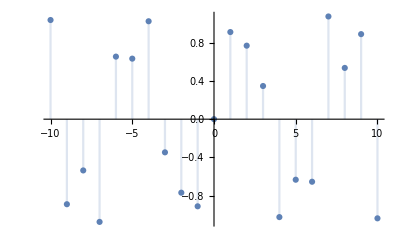

```mathematica
u[t_] := (10000 * UnitStep[t+0.0001] )- ( 10000 * UnitStep[t-0.0001]);
f[t_]:= Sin[t] + 0.5 * Sin[3 *t];
g[t_]:= (f[t] )* ( u[t]);
plot2=DiscretePlot[f[x],{x,−10,10}]
```

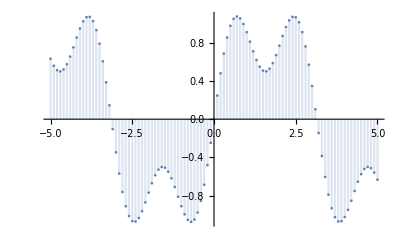

```mathematica
f[t_]:= Sin[t] + 0.5 * Sin[3 *t];
plot1=DiscretePlot[f[t],{t,−5,5,0.1}]
```

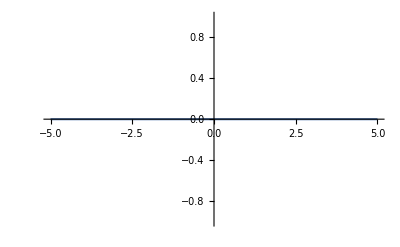

```mathematica
f[t_]:= Sin[t] + 0.5 * Sin[3 *t];
g[t] = f[n*(0.1)] * DiracDelta[t-n*(0.1)];
w[t]=Sum[g[t] ,{n,-Infinity,Infinity}];
Plot[w[t],{t,-5,5}]
```